```mathematica
Needs["NDSolve`FEM`"];
ClearAll[ sol,kappa,T0,Ptot,Pbkg,A,x,y,z,x0,y0,z0,sx,sy,Lzrad,Rrad, Lstick, Dstick,Lzstick, powerDensity3DFunc, powerDensity3D, copperCylinderRegion, copperStickRegion, copperRegion, meshRegion];
```

```mathematica
(*cpsInterFunc=Import["/home/hovanes/Documents/Wolfram\ Mathematica/CPS_Temperature_With_Mathematica/klcps_31b.m"]*)
```

```mathematica
powerDensity3DFunc[x_,y_,z_]:= Exp[- ((x-x0)^2/(2*sx^2)+(y-y0)^2/(2*sy^2))];
```

```mathematica
NormIntegral=Integrate[powerDensity3DFunc[x,y,z],{x,-∞,+∞},{y,-∞,+∞},{z,z0-Lzrad/2,z0+Lzrad/2}];
```

```mathematica
kappa=0.00385;T0=50.0; Pbkg=0.0001; Ptot=0.015; 
x0=0;y0=0; z0=0;sx=0.1;sy=0.1;
Lzrad=0.15; Rrad=1.0;
Lstick=100;Dstick=2;Lzstick=1;
```

```mathematica
powerDensity3D[x_,y_,z_]:=Pbkg+ Ptot/NormIntegral*powerDensity3DFunc[x,y,z]
```

```mathematica
NIntegrate[powerDensity3D[x,y,z],{x,x0-Rrad,x0+Rrad},{y,y0-Rrad,y0+Rrad},{z,z0-Lzrad/2,z0+Lzrad/2}]
```

0.015135

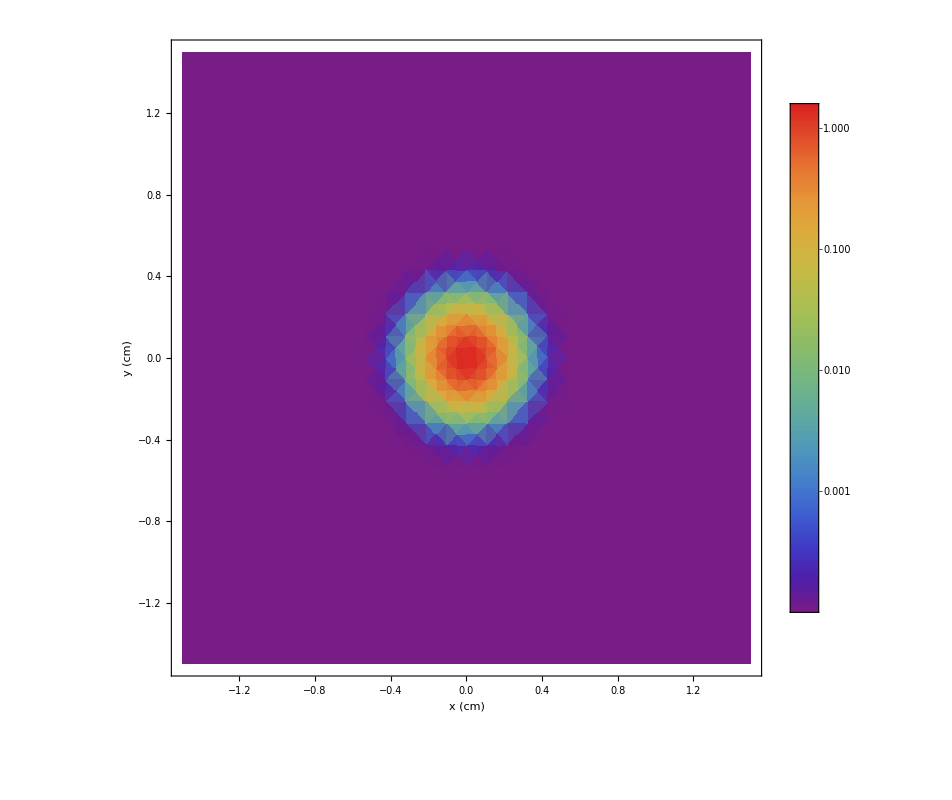

```mathematica
DensityPlot[powerDensity3D[x,y,z0],{x,x0-Rrad,x0+Rrad},{y,y0-Rrad,y0+Rrad},ColorFunction->{"Rainbow"},PlotRange->Full,PlotLegends->Automatic, ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"x (cm)", "y (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle->{17,GrayLevel[0],Italic},AspectRatio->1]
```

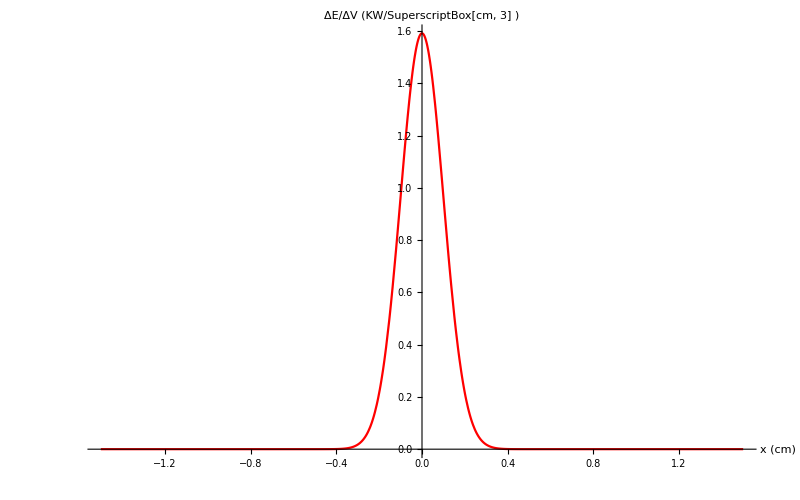

```mathematica
Plot[powerDensity3D[x,0,0],{x,x0-Rrad,x0+Rrad}, AxesLabel->{"x (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} ,LabelStyle->{17,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotRange->Full, PlotStyle->{Red,Thickness[0.002]}]
```

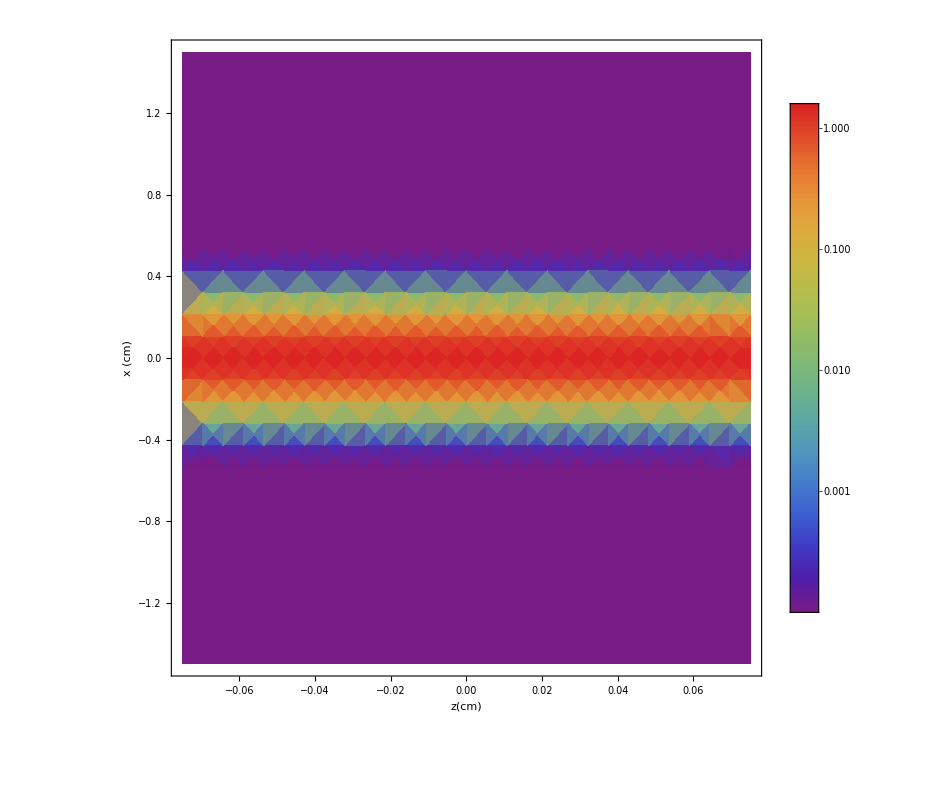

```mathematica
DensityPlot[powerDensity3D[x,y0,z],{z,z0-Lzrad/2,z0+Lzrad/2},{x,x0-Rrad,x0+Rrad},ColorFunction->"Rainbow",PlotRange->Full,PlotLegends->Automatic,ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"z(cm)", "x (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle->{17,GrayLevel[0],Italic},AspectRatio->1]
```

```mathematica
(*copperCylinderRegion=Cylinder[{{x0,y0,z0-Lzrad/2}, {x0,y0,z0+Lzrad/2}},Rrad];*)
```

```mathematica
(*RegionPlot3D[copperCylinderRegion, Mesh->None]*)
```

```mathematica
copperSquareRegion=Cuboid[{x0-Rrad,y0-Rrad,z0-Lzrad/2},{x0+Rrad,y0+Rrad,z0+Lzrad/2}];
(*RegionPlot3D[copperSquareRegion, Mesh->None]*)
```

```mathematica
copperStickRegion=Cuboid[{x0-Lstick,y0-Dstick/2,z0-Lzstick/2},{x0-Rrad,y0+Dstick/2,z0+Lzstick/2}];
```

```mathematica
copperRegion = RegionUnion[copperSquareRegion,copperStickRegion];
(*RegionPlot3D[copperRegion,Mesh->None]*)
```

```mathematica
boundaryMeshRegion=ToBoundaryMesh[copperRegion, MeshQualityGoal->"Maximal",(*"BoundaryMeshGenerator"->"Continuation",*) MaxBoundaryCellMeasure->{"Length"->0.03}];
(*boundaryMeshRegion["Wireframe"]*)
```

```mathematica
(*meshRegion=ToElementMesh[copperRegion, MeshQualityGoal->"Maximal",MaxCellMeasure->{"Volume"->0.3},  "BoundaryMeshGenerator"->"Continuation", MaxBoundaryCellMeasure->{"Length"->0.02}];*)
(*meshRegion["Wireframe"]*)
```

```mathematica
meshRegion=ToElementMesh[copperRegion,MeshQualityGoal->"Maximal",MaxBoundaryCellMeasure->{"Length"->0.03},MaxCellMeasure->{"Volume"->1}];
(*meshRegion["Wireframe"]*)
```

```mathematica
eqn=-Laplacian[u[x,y,z],{x,y,z}]==1/kappa*powerDensity3D[x,y,z]+ NeumannValue[0.0,{x,y,z}∈ boundaryMeshRegion] ;
```

```mathematica
sol=NDSolveValue[{eqn,DirichletCondition[u[x,y,z]==T0,(x==(x0-Lstick))]}, u,{x, y,z} ∈ meshRegion];
```

CompiledFunction::cfta: Argument {Boole[{-21.4811,1.,0.5}∈«1»],Boole[{-22.4387,1.,0.5}∈«1»],«47»,Boole[{-22.4387,-1.,0.277778}∈ElementMesh[{{-52.2918,1.,0.5},{-52.612,1.,0.5},{-52.2918,0.833333,0.5},{-52.612,0.833333,0.5},{-52.2918,1.,0.388889},{-52.612,1.,0.388889},{-52.2918,1.,0.277778},«37»,{-52.2918,-1.,0.5},{-52.612,-1.,0.5},{-52.2918,-1.,0.388889},{-52.612,-1.,0.388889},{-52.2918,-1.,0.277778},{-52.612,-1.,0.277778},«10166»},«9»,«1»,{PointElement[{{«1»},{«1»},{«1»},{«1»},«43»,{«1»},{«1»},{«1»},«10166»}]}]],«10640»} at position 1 should be a rank 1 tensor of machine-size integers.

```mathematica
(*sol=Import["/home/hovanes/Documents/Wolfram Mathematica/CPS_Temperature_With_Mathematica/t_radiator_solution_50CT0_100cmLong_1x2cm2Wide_1meshxp02bmesh.m"]*)
```

```mathematica
(*Export["/home/hovanes/Documents/Wolfram Mathematica/CPS_Temperature_With_Mathematica/t_radiator_solution_50CT0_100cmLong_1x2cm2Wide_p70meshFromp03bmesh.m", sol]*)
```

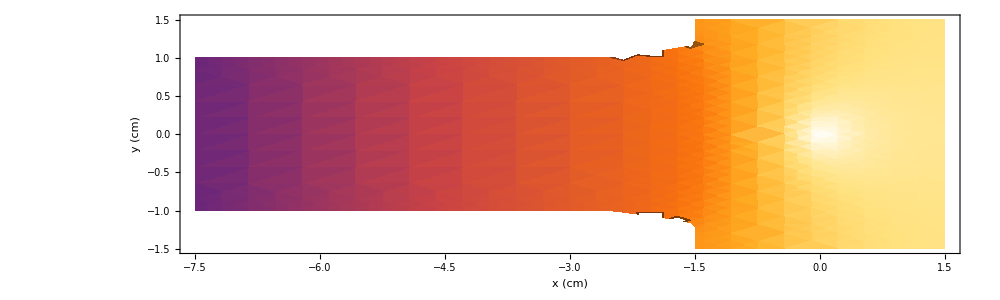

```mathematica
DensityPlot[sol[x,y,0], {x,x0-5*Rrad,x0+Rrad},{y,y0-Rrad,y0+Rrad},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{350,400},ImageSize->{1000,400},FrameLabel->{"x (cm)", "y (cm)", "T (^oC)"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->0.3]
```

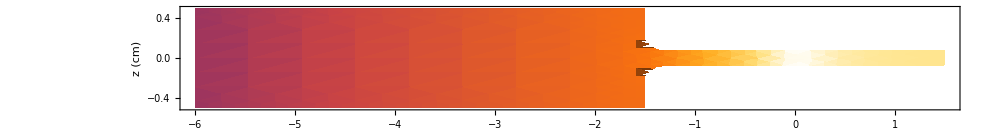

```mathematica
DensityPlot[sol[x,0,z], {x,x0-4*Rrad,x0+Rrad},{z,z0-Lzstick/1,z0+Lzstick/1},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{350,400},ImageSize->{1000,250},FrameLabel->{"x (cm)", "z (cm)", "T (^oC)"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->0.13]
```

```mathematica
SliceContourPlot3D[sol[x,y,z], "CenterPlanes",{x,x0-Lstick,x0+Rrad},{y,y0-Rrad,y0+Rrad},{z,z0-Lzrad/2,z0+Lzrad/2}, PlotTheme->"Detailed",PlotRange->Full,  ImageSize->{800,800},PlotLabel->"T (^oC)",AxesLabel->{ "x (cm)", "y (cm)","z (cm)"},LabelStyle->{22,GrayLevel[0],Italic}]
```

-Graphics3D-

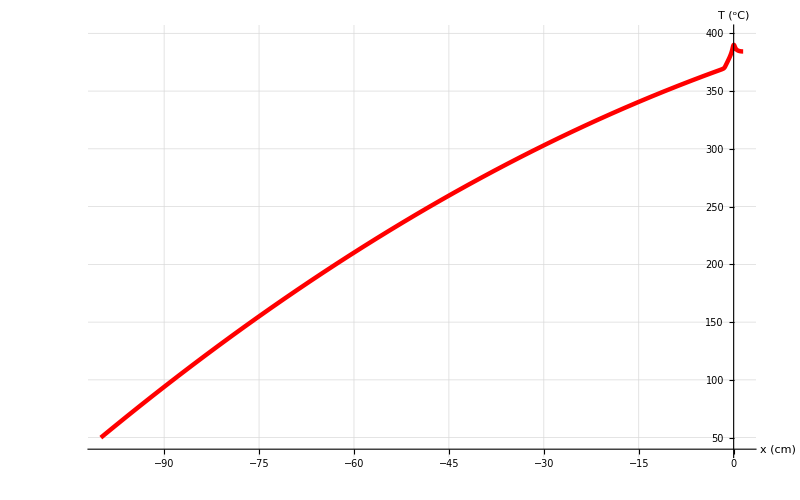

```mathematica
Plot[sol[x,y0,z0], {x,x0-Lstick,x0+Rrad},GridLines->Automatic,PlotRange->{T0-10,400},AxesLabel->{"x (cm)", "T (^oC)"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```

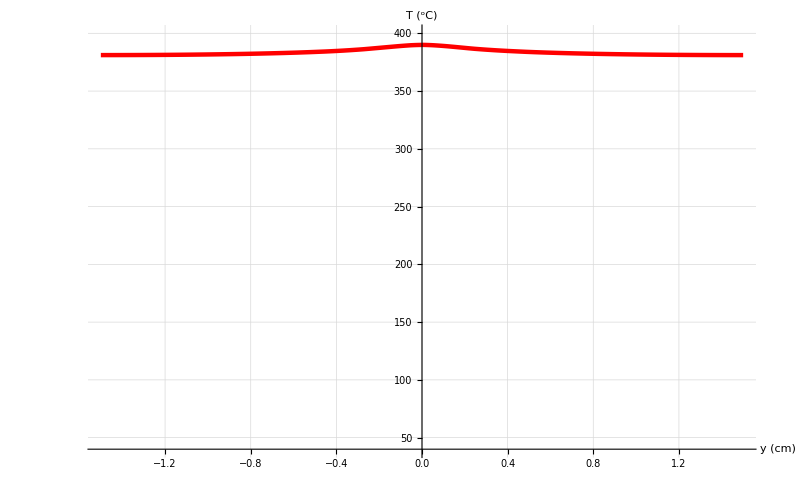

```mathematica
Plot[sol[x0,y,z0], {y,y0-Rrad,y0+Rrad},GridLines->Automatic,PlotRange->{T0-10,400},AxesLabel->{"y (cm)", "T (^oC)"} ,LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```